## Zestaw 1 (1 X 2021)

Zadanie 1.
Oblicz wynik dokładny i przybliżenie dziesiętne sumy do 15 miejsca po przecinku następujących wyrażeń:

```mathematica
(Cos(1110))/1.6+(970*99)/2.2^8
(√101)/(1+√37)
```

```mathematica
a=Cos[1110]/(16/10)+970*99/((22/10)^8)
N[a,15]
b=Sqrt[101]/(1+Sqrt[37])
N[b,15]
```

3410156250/19487171+(5 Cos[1110])/8

174.666658264231

(√101)/(1+√37)

1.4189203122553

Zadanie 2.
Z pomocą pętli For oblicz dla n=100:

```mathematica
∑_(i=1)^n (-1)^i i^2
```

```mathematica
s=0;
For[i=1,i≤100,i++,s+=(-1)^i * i*i];
s
```

5050

Zadanie 3.
Z pomocą pętli While oraz funkcji If oblicz sumę liczb pierwszych mniejszych od 100. (test czy liczba jest pierwsza można wykonać za pomocą funkcji PrimeQ)

```mathematica
s=0;
k=2;
While[k<100,If[PrimeQ[k],s+=k,s+=0];k++;]
s
```

1060

Zadanie 4.
Z pomocą dowolnej pętli oraz funkcji If wypisz te elementy x∈{0,1,2,...,100} dla których wyrażenie Cos(xπ/23) jest większe od 0.
Za pomocą funkcji DiscretePlot narysuj kolejne elementy ciągu:

{ Cos(xπ/23) |x∈{0,1,2,...,100} }

0

1

2

3

4

5

6

7

8

9

10

11

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

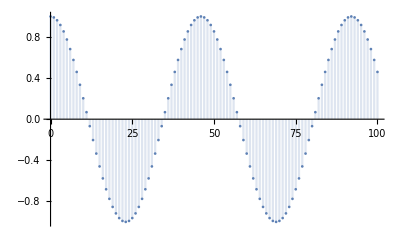

```mathematica
For[x=0,x≤100,x++,If[Cos[x Pi/23]>0,Print[x]]]
DiscretePlot[Cos[n Pi/23],{n,0,100}]
```

Zadanie 5.
Zdefiniuj funkcję :

f(x)=Sin(x)-x^2+0.1

podaj wartość funkcji f w punktach x= 2 i x=π/2

narysuj wykres funkcji (Plot) i odczytaj z wykresu czy funkcja ma miejsca zerowe w przedziale [0,1]? Jeśli tak to ile?

1/10-x^2+Sin[x]

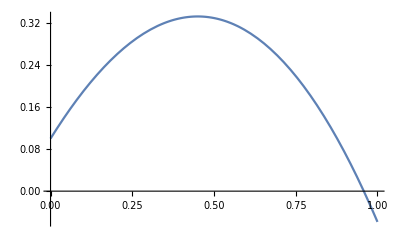

```mathematica
Clear[x]
f[x_]=Sin[x]-x x+1/10
Plot[f[x],{x,0,1}]
```

Zadanie 6.
Wykorzystując instrukcję “If” zdefiniuj następującą funkcję:

```mathematica
g(x)=Piecewise[{{x^5-4x+1, x<0}, {x^2+1, x≥0}}]
```

podaj wartość wyrażenia: g(-4) - g(6)

narysuj wykres

-1044

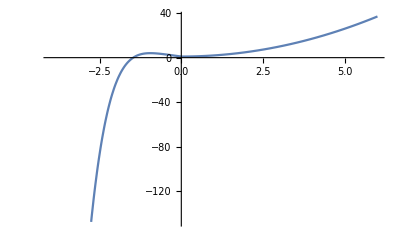

```mathematica
Clear[x]
g[x_]=Piecewise[{{x^5-4x+1,x<0},{x x+1,x≥0}}];
g[-4]-g[6]
Plot[g[x],{x,-4,6}]
```